```mathematica
Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
(* If given a list of files*)
GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
association=Append[association,rawFile[[k]][[1]]->StringJoin[DeleteCases[Take[rawFile[[k]],{2,-1}],Null]]];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];

FourierFit[list_,rev_]:=Module[{fit,function,dataPts,stepSize,dataPtsPerRev,angles,data(*,C0,C2,C4,S2,S4*)},

function[θ_]= C0+C2 Cos[2(θ+θo)]+C4 Cos[4(θ+θo)]+S2 Sin[2(θ+θo)]+S4 Sin[4(θ+θo)];
dataPts=Length[list];
dataPtsPerRev=dataPts/rev;
angles=Range[0,(2π*rev)-2π/dataPtsPerRev,2π/dataPtsPerRev];
data=Transpose[{list,angles}];
fit=NonlinearModelFit[data,function[θ],{{C0,1000},C2,C4,S2,S4,θo},θ]
];


DFT[list_,rev_]:=Module[{numItems,i,k,j,reconstructionCos,reconstructionSin,returnCos,errorsCos,returnSin,errorsSin,intensity},
returnCos={};
errorsCos={};
returnSin={};
errorsSin={};
reconstructionCos={};
reconstructionSin={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnCos,0];
AppendTo[returnSin,0];

];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnCos[[k+1]]=N[returnCos[[k+1]]+1/numItems*intensity*Cos[2*π *k *rev* (i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems]];,
returnCos[[k+1]]=N[returnCos[[k+1]]+2/numItems*intensity*Cos[2*π *k* rev *(i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems]];
];
];
];
(*

For[j=0,j<numItems/2,j++,
AppendTo[errorsSin,0];
AppendTo[errorsCos,0];
For[i=1,i<=numItems,i++,
intensity=list[[i]];
AppendTo[reconstructionCos,0];
AppendTo[reconstructionSin,0];
reconstructionCos[[i]]=intensity/Cos[2*π*j*rev*(i)/numItems] ;
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]=intensity/Sin[2*π*1.0001*j*rev*(i)/numItems];];
For [k=0,k<numItems/2,k++,
If[k≠j,
reconstructionCos[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(i)/numItems] )/Cos[2*π*j*rev*(i)/numItems];
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(1)/numItems] )/Sin[2*π*1.0001*j*rev*(i)/numItems]];
];
];
errorsSin[[j+1]]+=Power[reconstructionSin[[i]]-returnSin[[j+1]],2];
errorsCos[[j+1]]+=Power[reconstructionCos[[i]]-returnCos[[j+1]],2];
];
errorsSin[[j+1]]=Sqrt[errorsSin[[j+1]]/numItems];
errorsCos[[j+1]]=Sqrt[errorsCos[[j+1]]/numItems];
];
*)
{{returnSin,errorsSin},{returnCos,errorsCos}}
];

StokesParametersFromFourierData[intensityArray_,rev_,alpha_,beta0_,delta_]:=
Module[{fc(*Fourrier Coefficients*),c0,c2,c4,s2,s4,stokes},
fc=DFT[intensityArray,rev];
stokes={0,0,0,0,0,0};
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
stokes[[1]]=c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0]);
stokes[[2]]=2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[3]]=2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[4]]=Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]]);
stokes[[5]]=c2/(Sin[delta]Sin[2 alpha + 4 beta0]stokes[[1]]);
stokes[[6]]=-s2/(Sin[delta]Cos[2 alpha + 4 beta0]stokes[[1]]);
stokes

];
StokesParametersFromPolFile[polFile_,alpha_,beta0_,delta_]:=
Module[{intensityArray,f,rev},
f=ImportFile[polFile];
intensityArray=Normal[f[[2]][All,"COUNT"]];
rev=f[[1]]["#REV:"];
StokesParametersFromFourierData[intensityArray,rev,alpha,beta0,delta]
];

GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];

AverageDarkCountsRate[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/nCycles^2*dwell^2;
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];
DarkCountsRate[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/nCycles^2*dwell^2;
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageBackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=DarkCountsRate[darkCountsFiles];
Print[darkCountsRate];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

BackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=DarkCountsRate[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageSignalRateCurrentNorm[files_,molyCountsRate_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,rev,j},
darkCountsRate=DarkCountsRate[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
rev=files[[i]][[1]]["#REV:"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/rev/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/rev/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/rev/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*rev^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*rev^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2*rev^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

SignalRateCurrentNormFromFiles[file_,molyCountFiles_,darkCountsFiles_]:=Module[{molyCountsRate,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=AverageDarkCountsRate[darkCountsFiles];
molyCountsRate=AverageBackgroundRateCurrentNorm[molyCountFiles,darkCountsFiles];
SignalRateCurrentNormFromRates[file,molyCountFiles,darkCountsFiles]
];

SignalRateCurrentNormFromRates[fileName_,molyCountsRate_,darkCountsRate_]:=Module[{file,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
file=ImportFile[fileName];
nDataPts=Length[Normal[file[[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
counts=Normal[file[[2]][All,"COUNT"]];
current=Normal[file[[2]][All,"CURRENT"]];
dwell=file[[1]]["#DWELL(s):"];
nCycles=file[[1]]["#REV:"];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2);
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

CalculateOneFileStokes[polFileName_,molyCountRate_,darkCountRate_,alpha_,beta_,delta_]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["#REV:"];
signal=SignalRateCurrentNormFromRates[polFileName,molyCountRate,darkCountRate];
StokesParametersFromFourierData[signal[[1]],rev,alpha,beta,delta]
];

AverageStokes[stokesVectors_]:=Module[{transposedValues,stokes,stokesStdDev},
stokes=stokesVectors[[1]];
stokesStdDev=stokes;
transposedValues=Transpose[stokesVectors];
For[i=1,i≤Length[stokesVectors[[1]]],i++,
stokes[[i]]=Mean[transposedValues[[i]]];
stokesStdDev[[i]]=StandardDeviation[transposedValues[[i]]]/Sqrt[Length[transposedValues]];
];
{stokes,stokesStdDev}
];

CalculateAverageStokes[polFileNames_,molyCountRate_,darkCountRate_,alpha_,beta_,delta_]:=Module[{signal,stokes,stokesStdDev,file,rev,j,i,stokesValues,transposedValues},
stokes={0,0,0,0,0,0};
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],molyCountRate,darkCountRate,alpha,beta,delta];
AppendTo[stokesValues,stokes]
];
AverageStokes[stokesValues];
]

NormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]/intensity;
];
newVector
];

UnNormalizeStokes[stokesVector_]:=Module[{intensity,newVector,i},
newVector=stokesVector;
intensity=stokesVector[[1]];
For[i=2,i≤Length[stokesVector],i++,
newVector[[i]]=stokesVector[[i]]*intensity;
];
newVector
];

SubtractStokes[addedStokes_,subtractedStokes_]:=Module[
{unNormAdd,unNormSub},
unNormAdd=UnNormalizeStokes[addedStokes];
unNormSub=UnNormalizeStokes[subtractedStokes];
NormalizeStokes[unNormAdd-unNormSub]
];
```

```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-12-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dropBoxfolderLaptop=FileNameJoin[{"/","home","karl","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","DataRuns"}];
folder=FileNameJoin[{dropBoxfolderLaptop,dataFolder}];
SetDirectory[folder];
FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,dataDump,wavemeterOffsets}

```mathematica
SetDirectory[FileNameJoin[{folder,"18-01-04_PolarizingElectrons"}]];
names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]]
```

{POL2018-01-04_210629.dat,POL2018-01-04_210843.dat,POL2018-01-04_211059.dat,POL2018-01-04_211316.dat,POL2018-01-04_211532.dat,POL2018-01-04_211750.dat,POL2018-01-04_212005.dat,POL2018-01-04_212223.dat,POL2018-01-04_212439.dat,POL2018-01-04_212655.dat,POL2018-01-04_212912.dat,POL2018-01-04_213128.dat,POL2018-01-04_213346.dat,POL2018-01-04_213601.dat,POL2018-01-04_213820.dat,POL2018-01-04_214036.dat,POL2018-01-04_214253.dat,POL2018-01-04_214510.dat,POL2018-01-04_214726.dat,POL2018-01-04_214943.dat,POL2018-01-04_215159.dat,POL2018-01-04_215417.dat,POL2018-01-04_215632.dat,POL2018-01-04_215849.dat,POL2018-01-04_220106.dat,POL2018-01-04_220322.dat,POL2018-01-04_220539.dat,POL2018-01-04_220755.dat,POL2018-01-04_221013.dat,POL2018-01-04_221228.dat,POL2018-01-04_221445.dat,POL2018-01-04_221702.dat,POL2018-01-04_221918.dat,POL2018-01-04_222135.dat,POL2018-01-04_222351.dat,POL2018-01-04_222609.dat,POL2018-01-04_222824.dat,POL2018-01-04_223041.dat,POL2018-01-04_223258.dat,POL2018-01-04_223514.dat,POL2018-01-04_223731.dat,POL2018-01-04_223947.dat,POL2018-01-04_224205.dat,POL2018-01-04_224420.dat,POL2018-01-04_224637.dat,POL2018-01-04_224854.dat,POL2018-01-04_225110.dat,POL2018-01-04_225327.dat,POL2018-01-04_225543.dat,POL2018-01-04_225801.dat,POL2018-01-04_230016.dat,POL2018-01-04_230233.dat,POL2018-01-04_230450.dat,POL2018-01-04_230706.dat,POL2018-01-04_230923.dat,POL2018-01-04_231139.dat,POL2018-01-04_231358.dat,POL2018-01-04_231614.dat,POL2018-01-04_231831.dat,POL2018-01-04_232048.dat,POL2018-01-04_232304.dat,POL2018-01-04_232521.dat,POL2018-01-04_232737.dat,POL2018-01-04_232955.dat,POL2018-01-04_233212.dat,POL2018-01-04_233428.dat,POL2018-01-04_233646.dat,POL2018-01-04_233902.dat,POL2018-01-04_234119.dat,POL2018-01-04_234335.dat}

```mathematica
GetIndexOfFilenameFromTimestamp[names,"122503"]
```

7

```mathematica
list=Join[{"This",,"is",,"Stringjoin!"}]
DeleteCases[list,Null]
```

{This,Null,is,Null,Stringjoin!}

{This,is,Stringjoin!}

```mathematica
runs=5;
energies={30};
startFile=GetIndexOfFilenameFromTimestamp[names,"122503"];
energyXdarkFileNames={};
For[i=startFile,i<Length[energies]+startFile,i++,
fileNames=Take[names,{i,i+Length[energies]*runs-1,Length[energies]}];
AppendTo[energyXdarkFileNames,fileNames];
];

energyXdarkFileNames

averagedDark={};
energyXdarkFiles={};

For[j=1,j<=Length[energyXdarkFileNames],j++,
files=ImportFile[energyXdarkFileNames[[j]]];
AppendTo[energyXdarkFiles,files];
(* A "File" here means a list consisting of two elements. The first element is a list of associations containing information pertinent to all of the datapoints, the "header." The second element is the dataset.*)
averageDark=N[DarkCountsRate[files]];
AppendTo[averagedDark,averageDark];
];

averagedDark
```

{{POL2018-01-03_122503.dat,POL2018-01-03_122822.dat,POL2018-01-03_123142.dat,POL2018-01-03_123502.dat,POL2018-01-03_123822.dat}}

```mathematica
{{{{13.533333333333333},{13.6},{16.066666666666666},{14.333333333333334},{13.666666666666666},{12.933333333333334},{13.933333333333334},{14.2},{14.133333333333333},{14.2},{12.466666666666667},{12.733333333333333},{13.4},{15.333333333333334},{12.533333333333333},{13.866666666666667},{14.666666666666666},{14.8},{17.},{14.266666666666667},{16.2},{13.733333333333333},{12.466666666666667},{14.466666666666667},{13.},{12.533333333333333},{13.6},{11.2},{14.4},{16.933333333333334},{15.6},{16.466666666666665},{14.333333333333334},{15.2},{15.},{15.066666666666666},{13.466666666666667},{15.466666666666667},{12.733333333333333},{12.066666666666666},{11.133333333333333},{12.333333333333334},{13.066666666666666},{13.333333333333334},{12.333333333333334},{12.8},{13.533333333333333},{14.066666666666666},{14.866666666666667},{14.933333333333334},{15.6},{14.133333333333333},{16.866666666666667},{12.933333333333334},{13.333333333333334},{11.933333333333334},{13.666666666666666},{12.533333333333333},{11.866666666666667},{13.4}},{{8.548684109265004},{8.56971411425142},{9.314504817756013},{8.79772697916911},{8.590692637965812},{8.357032966310472},{8.674099376880577},{8.756711711595853},{8.73613186713662},{8.756711711595853},{8.204876598706406},{8.292164976651152},{8.506468127254696},{9.09945053286186},{8.226785520481252},{8.653323061113573},{8.899438184514796},{8.939798655450803},{9.581231653602787},{8.777243302996675},{9.353074360871938},{8.611620056644394},{8.204876598706406},{8.83855191759374},{8.378544026261364},{8.226785520481252},{8.56971411425142},{7.776888838089432},{8.818163074019441},{9.562426470305537},{9.178235124467012},{9.429740187301027},{8.79772697916911},{9.0598013223249},{9.},{9.019977827023745},{8.527602242131136},{9.13892772703669},{8.292164976651152},{8.072174428244226},{7.753708789992051},{8.160882305241266},{8.4},{8.485281374238571},{8.160882305241266},{8.31384387633061},{8.548684109265004},{8.71550342780037},{8.959910713840847},{8.97997772825746},{9.178235124467012},{8.73613186713662},{9.543584232352119},{8.357032966310472},{8.485281374238571},{8.027452896155792},{8.590692637965812},{8.226785520481252},{8.0049984384758},{8.506468127254696}}}}
```

```mathematica
SetDirectory[FileNameJoin[{folder,"18-01-04_PolarizingElectrons"}]];
names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]]
```

{POL2018-01-04_210629.dat,POL2018-01-04_210843.dat,POL2018-01-04_211059.dat,POL2018-01-04_211316.dat,POL2018-01-04_211532.dat,POL2018-01-04_211750.dat,POL2018-01-04_212005.dat,POL2018-01-04_212223.dat,POL2018-01-04_212439.dat,POL2018-01-04_212655.dat,POL2018-01-04_212912.dat,POL2018-01-04_213128.dat,POL2018-01-04_213346.dat,POL2018-01-04_213601.dat,POL2018-01-04_213820.dat,POL2018-01-04_214036.dat,POL2018-01-04_214253.dat,POL2018-01-04_214510.dat,POL2018-01-04_214726.dat,POL2018-01-04_214943.dat,POL2018-01-04_215159.dat,POL2018-01-04_215417.dat,POL2018-01-04_215632.dat,POL2018-01-04_215849.dat,POL2018-01-04_220106.dat,POL2018-01-04_220322.dat,POL2018-01-04_220539.dat,POL2018-01-04_220755.dat,POL2018-01-04_221013.dat,POL2018-01-04_221228.dat,POL2018-01-04_221445.dat,POL2018-01-04_221702.dat,POL2018-01-04_221918.dat,POL2018-01-04_222135.dat,POL2018-01-04_222351.dat,POL2018-01-04_222609.dat,POL2018-01-04_222824.dat,POL2018-01-04_223041.dat,POL2018-01-04_223258.dat,POL2018-01-04_223514.dat,POL2018-01-04_223731.dat,POL2018-01-04_223947.dat,POL2018-01-04_224205.dat,POL2018-01-04_224420.dat,POL2018-01-04_224637.dat,POL2018-01-04_224854.dat,POL2018-01-04_225110.dat,POL2018-01-04_225327.dat,POL2018-01-04_225543.dat,POL2018-01-04_225801.dat,POL2018-01-04_230016.dat,POL2018-01-04_230233.dat,POL2018-01-04_230450.dat,POL2018-01-04_230706.dat,POL2018-01-04_230923.dat,POL2018-01-04_231139.dat,POL2018-01-04_231358.dat,POL2018-01-04_231614.dat,POL2018-01-04_231831.dat,POL2018-01-04_232048.dat,POL2018-01-04_232304.dat,POL2018-01-04_232521.dat,POL2018-01-04_232737.dat,POL2018-01-04_232955.dat,POL2018-01-04_233212.dat,POL2018-01-04_233428.dat,POL2018-01-04_233646.dat,POL2018-01-04_233902.dat,POL2018-01-04_234119.dat,POL2018-01-04_234335.dat}

```mathematica
numberOfDistinctRuns=7;
noPumpBackground=Take[names,{1,-1,numberOfDistinctRuns}]
noPumpExcited=Take[names,{2,-1,numberOfDistinctRuns}]
noPumpThreshold=Take[names,{3,-1,numberOfDistinctRuns}];
sPlusExcited=Take[names,{4,-1,numberOfDistinctRuns}];
sPlusThreshold=Take[names,{5,-1,numberOfDistinctRuns}];
sMinusExcited=Take[names,{6,-1,numberOfDistinctRuns}];
sMinusThreshold=Take[names,{7,-1,numberOfDistinctRuns}];
```

```mathematica
runs=5;
energies={30};
startFile=17;
energyXmolyFileNames={};

For[i=startFile,i<Length[energies]+startFile,i++,
fileNames=Take[names,{i,i+Length[energies]*runs-1,Length[energies]}];
AppendTo[energyXmolyFileNames,fileNames];
];

energyXmolyFileNames=noPumpBackground
```

{POL2018-01-04_210629.dat,POL2018-01-04_212223.dat,POL2018-01-04_213820.dat,POL2018-01-04_215417.dat,POL2018-01-04_221013.dat,POL2018-01-04_222609.dat,POL2018-01-04_224205.dat,POL2018-01-04_225801.dat,POL2018-01-04_231358.dat,POL2018-01-04_232955.dat}

```mathematica
averagedMolyDarkSubtracted={};

For[j=1,j≤Length[energyXmolyFileNames],j++,
files=ImportFile[energyXmolyFileNames[[j]]];
averageMolyDarkSubtracted=N[AverageBackgroundRateCurrentNorm[files,energyXdarkFiles[[j]]]];
AppendTo[averagedMolyDarkSubtracted,averageMolyDarkSubtracted];
];
averagedMolyDarkSubtracted
```

StringJoin::string: String expected at position 1 in StringJoin[0.000113].

StringJoin::string: String expected at position 1 in StringJoin[0.127].

StringJoin::string: String expected at position 1 in StringJoin[0.000877].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{{{203/15},{68/5},{241/15},{43/3},{41/3},{194/15},{209/15},{71/5},{212/15},{71/5},{187/15},{191/15},{67/5},{46/3},{188/15},{208/15},{44/3},{74/5},{17},{214/15},{81/5},{206/15},{187/15},{217/15},{13},{188/15},{68/5},{56/5},{72/5},{254/15},{78/5},{247/15},{43/3},{76/5},{15},{226/15},{202/15},{232/15},{191/15},{181/15},{167/15},{37/3},{196/15},{40/3},{37/3},{64/5},{203/15},{211/15},{223/15},{224/15},{78/5},{212/15},{253/15},{194/15},{40/3},{179/15},{41/3},{188/15},{178/15},{67/5}},{{(3 √203)/5},{(6 √51)/5},{(3 √241)/5},{3 √(43/5)},{3 √(41/5)},{(3 √194)/5},{(3 √209)/5},{(3 √213)/5},{(6 √53)/5},{(3 √213)/5},{(3 √187)/5},{(3 √191)/5},{(3 √201)/5},{3 √(46/5)},{(6 √47)/5},{(12 √13)/5},{6 √(11/5)},{(3 √222)/5},{3 √(51/5)},{(3 √214)/5},{(27 √3)/5},{(3 √206)/5},{(3 √187)/5},{(3 √217)/5},{3 √(39/5)},{(6 √47)/5},{(6 √51)/5},{(6 √42)/5},{(18 √6)/5},{(3 √254)/5},{(9 √26)/5},{(3 √247)/5},{3 √(43/5)},{(6 √57)/5},{9},{(3 √226)/5},{(3 √202)/5},{(6 √58)/5},{(3 √191)/5},{(3 √181)/5},{(3 √167)/5},{3 √(37/5)},{42/5},{6 √2},{3 √(37/5)},{(24 √3)/5},{(3 √203)/5},{(3 √211)/5},{(3 √223)/5},{(12 √14)/5},{(9 √26)/5},{(6 √53)/5},{(3 √253)/5},{(3 √194)/5},{6 √2},{(3 √179)/5},{3 √(41/5)},{(6 √47)/5},{(3 √178)/5},{(3 √201)/5}}}

Part::partw: Part 3 of Run1,bias=100.1,target=2.0,sweep=0.9,pump=pi[All,COUNT] does not exist.

Part::partw: Part 3 of Run1,bias=100.1,target=2.0,sweep=0.9,pump=pi[All,CURRENT] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {34/5} {1/Abs[MessageTemplate:>Dataset::partatomic],1/Abs[MessageParameters→<|Type→TypeSystem`Atom[Real],Part→CURRENT,Symbol→Part|>]} cannot be combined.

Thread::tdlen: Objects of unequal length in -{34/5} {1/Abs[MessageTemplate:>Dataset::partatomic],1/Abs[MessageParameters→<|Type→TypeSystem`Atom[Real],Part→CURRENT,Symbol→Part|>]} cannot be combined.

Thread::tdlen: Objects of unequal length in … cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::partd: Part specification 2⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{All/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+All/(2 2⟦1⟧[#DWELL(s):]),COUNT/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+COUNT/(2 2⟦1⟧[#DWELL(s):])},{√(1/4 All ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 All (2⟦1⟧[#DWELL(s):])^2),√(1/4 COUNT ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 COUNT (2⟦1⟧[#DWELL(s):])^2)}}

{{All/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+All/(2 3⟦1⟧[#DWELL(s):]),COUNT/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+COUNT/(2 3⟦1⟧[#DWELL(s):])},{√(1/4 All ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 All (3⟦1⟧[#DWELL(s):])^2),√(1/4 COUNT ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 COUNT (3⟦1⟧[#DWELL(s):])^2)}}

{{All/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+All/(2 4⟦1⟧[#DWELL(s):]),COUNT/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+COUNT/(2 4⟦1⟧[#DWELL(s):])},{√(1/4 All ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 All (4⟦1⟧[#DWELL(s):])^2),√(1/4 COUNT ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 COUNT (4⟦1⟧[#DWELL(s):])^2)}}

{{All/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+All/(2 5⟦1⟧[#DWELL(s):]),COUNT/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+COUNT/(2 5⟦1⟧[#DWELL(s):])},{√(1/4 All ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 All (5⟦1⟧[#DWELL(s):])^2),√(1/4 COUNT ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 COUNT (5⟦1⟧[#DWELL(s):])^2)}}

{{All/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+All/(2 6⟦1⟧[#DWELL(s):]),COUNT/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+COUNT/(2 6⟦1⟧[#DWELL(s):])},{√(1/4 All ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 All (6⟦1⟧[#DWELL(s):])^2),√(1/4 COUNT ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 COUNT (6⟦1⟧[#DWELL(s):])^2)}}

{{All/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+All/(2 7⟦1⟧[#DWELL(s):]),COUNT/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+COUNT/(2 7⟦1⟧[#DWELL(s):])},{√(1/4 All ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 All (7⟦1⟧[#DWELL(s):])^2),√(1/4 COUNT ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 COUNT (7⟦1⟧[#DWELL(s):])^2)}}

{{All/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+All/(2 8⟦1⟧[#DWELL(s):]),COUNT/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+COUNT/(2 8⟦1⟧[#DWELL(s):])},{√(1/4 All ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 All (8⟦1⟧[#DWELL(s):])^2),√(1/4 COUNT ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 COUNT (8⟦1⟧[#DWELL(s):])^2)}}

{{All/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+All/(2 9⟦1⟧[#DWELL(s):]),COUNT/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+COUNT/(2 9⟦1⟧[#DWELL(s):])},{√(1/4 All ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 All (9⟦1⟧[#DWELL(s):])^2),√(1/4 COUNT ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 COUNT (9⟦1⟧[#DWELL(s):])^2)}}

{{All/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+All/(2 10⟦1⟧[#DWELL(s):]),COUNT/(2 {{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])+COUNT/(2 10⟦1⟧[#DWELL(s):])},{√(1/4 All ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 All (10⟦1⟧[#DWELL(s):])^2),√(1/4 COUNT ({{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122503.dat},#Comments→{Run,1,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_122822.dat},#Comments→{Run,2,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.0000907},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{110.},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123142.dat},#Comments→{Run,3,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000146},#CURTEMP_R(degC):→{50.3},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123502.dat},#Comments→{Run,4,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]},{<|#File→{/home/pi/RbData/2018-01-03/POL2018-01-03_123822.dat},#Comments→{Run,5,,Room,lights,off.,dark,counts,(no,gas),background.},#IonGauge(Torr):→{0.000093},#CVGauge(N2)(Torr):→{0.102},#CVGauge(He)(Torr):→{0.000115},#CURTEMP_R(degC):→{50.2},#SETTEMP_R(degC):→{0.},#CURTEMP_T(degC):→{109.9},#SETTEMP_T(degC):→{110.},#AOUT:→{0},#LEAKCURR:→{0.0001},#AOUTCONV:→{0.030938},#REV:→{1},#DATAPPR:→{60},#STPPERREV:→{1200},#DATPTS:→{60},#DWELL(s):→{3}|>,Dataset[<>]}}[#DWELL(s):])^2+1/4 COUNT (10⟦1⟧[#DWELL(s):])^2)}}

{1}
 |  |  |  |

```mathematica
runs=5;
energies={30};
startFile=12;
energyXsignalFileNames={};
For[i=startFile,i<Length[energies]+startFile,i++,
fileNames=Take[names,{i,i+Length[energies]*runs-1,Length[energies]}];
AppendTo[energyXsignalFileNames,fileNames];
];

energyXsignalFileNames
```

{{POL2018-01-03_125059.dat,POL2018-01-03_125418.dat,POL2018-01-03_125738.dat,POL2018-01-03_130058.dat,POL2018-01-03_130418.dat}}

```mathematica
averagedSignalBackgroundSubtracted={};


For[j=1,j≤Length[energyXsignalFileNames],j++,
files=ImportFile[energyXsignalFileNames[[j]]];
averageSignalBackgroundSubtracted=N[AverageSignalRateCurrentNorm[files,averagedMolyDarkSubtracted[[j]],energyXdarkFiles[[j]]]];
AppendTo[averagedSignalBackgroundSubtracted,averageSignalBackgroundSubtracted];
];
averagedSignalBackgroundSubtracted
```

{{{38.9902,36.3537,39.7456,35.2209,36.2591,36.5337,37.3689,36.0771,34.6125,42.6469,40.2367,40.3283,38.0415,40.839,39.1162,39.8493,39.8393,36.1532,38.7406,37.5981,35.7093,35.4742,36.3048,37.24,37.545,40.6764,41.6343,40.201,43.757,41.2931,41.1939,37.7497,43.0405,42.2627,37.561,39.4444,38.8498,37.9134,39.2782,43.2528,40.692,41.8609,39.5109,41.8496,43.1209,43.8445,40.4393,45.5396,42.0842,41.1515,43.6403,41.3303,39.0058,43.5229,40.6735,43.3877,43.3057,44.7773,43.882,44.5388},{1.2848,1.25179,1.26174,1.2197,1.2437,1.24874,1.26004,1.23256,1.2134,1.306,1.29625,1.29411,1.26522,1.28343,1.29545,1.27688,1.28689,1.22927,1.24239,1.25237,1.20701,1.22541,1.22974,1.21875,1.23898,1.29626,1.29006,1.28789,1.32199,1.26765,1.26841,1.21651,1.31185,1.28206,1.22514,1.23804,1.25485,1.22008,1.26735,1.32139,1.26306,1.28688,1.25426,1.28722,1.30027,1.30685-0.00571186 ⅈ,1.2685,1.33214-0.00536421 ⅈ,1.27971,1.26469,1.30107-0.00950243 ⅈ,1.27318,1.22831-0.011025 ⅈ,1.3012,1.25832,1.29969,1.29891,1.29848-0.0197667 ⅈ,1.31339,1.32002}}}

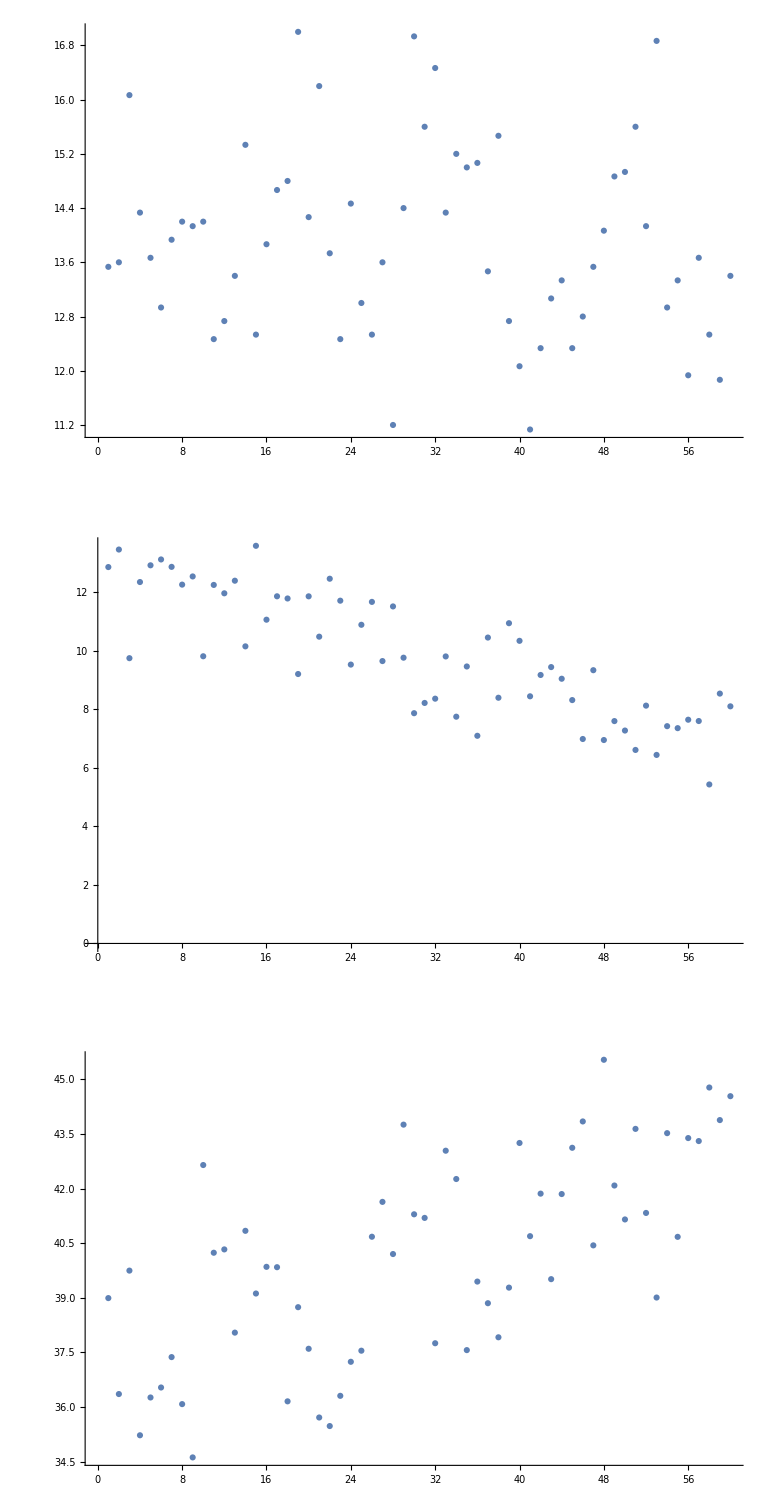

```mathematica
darkPlotData={};
molyPlotData={};
signalPlotData={};
For[i=1,i≤Length[energies],i++,
AppendTo[darkPlotData,averagedDark[[i]][[1]]];
AppendTo[molyPlotData,averagedMolyDarkSubtracted[[i]][[1]]];
AppendTo[signalPlotData,averagedSignalBackgroundSubtracted[[i]][[1]]];
];
darkPlots=ListPlot[darkPlotData];
molyPlots=ListPlot[molyPlotData];
signalPlots=ListPlot[signalPlotData];
GraphicsGrid[{{darkPlots},{molyPlots},{signalPlots}}]
```

```mathematica
alphaOld=3.2*π/180;
betaOld=-6.95*π/180;
deltaAB=alpha-beta;
delta=90*π/180;
```

```mathematica
alpha=20.4*π/180;
beta=63.3*π/180;
deltaAB=alpha-beta;
delta=90*π/180;


stokesAverages={};
stokesStdMs={};
energy=energies

For[j=1,j≤Length[energy],j++,
runs={};
signal=energyXsignalFileNames[[j]];
molyCounts=averagedMolyDarkSubtracted[[j]];
darkCounts=averagedDark[[j]];

For[i=1,i≤Length[signal],i++,
subtracted=SignalRateCurrentNormFromRates[signal[[i]],molyCounts,darkCounts];
AppendTo[runs,subtracted];
];

stokesData={};
For[i=1,i≤Length[signal],i++,
stokes=StokesParametersFromFourierData[runs[[i]][[1]],1,alpha,beta,delta];
AppendTo[stokesData,stokes];
];

stokesAverage=AverageStokes[stokesData];(*Stokes average returns a vector where the first argument is a vector containing the average stokes parameters and the second argument is a vector containing the standard deviations of the mean of the values.*)
AppendTo[stokesAverages,stokesAverage[[1]]];
AppendTo[stokesStdMs,stokesAverage[[2]]];
]

(*belowThresholdStokes=Take[stokesAverages,{-2,-1}];
belowThresholdAverageStokes=AverageStokes[belowThresholdStokes]*)


For[j=1,j≤Length[energy]-Length[belowThresholdAverageStokes],j++,
stokesAverages[[j]]=SubtractStokes[stokesAverages[[j]],belowThresholdAverageStokes[[1]]];
];



stokesParam={};
energyStokesWError={};
For[j=1,j≤Length[stokesAverage[[1]]],j++,(*The Stokes parameters loop over # of stokes*)
stokesIndex=j;
px={};
For[i=1,i≤Length[energy],i++,(* The energy Loop, over number of energies*)
AppendTo[px,stokesAverages[[i]][[j]]];
];
AppendTo[stokesParam,px];
errorBars={};
For[i=1,i≤Length[energy],i++,(* The energy Loop, over number of energies*)
AppendTo[errorBars,ErrorBar[stokesStdMs[[i]][[j]]]];
];
(*errorBars={ErrorBar[stokesStdMs[[1]][[j]]],ErrorBar[stokesStdMs[[2]][[j]]],ErrorBar[stokesStdMs[[3]][[j]]]};*)
energyVsPx={};
For[i=1,i≤Length[energy],i++,(* The energy Loop, over number of energies*)
AppendTo[energyVsPx,{Transpose[{energy,stokesParam[[j]]}][[i]],errorBars[[i]]}];
];
AppendTo[energyStokesWError,energyVsPx];
];
```

{30}

```mathematica
yRange={-.1,.1};
p1=ErrorListPlot[energyStokesWError[[2]],PlotLabel->"P1 vs. Incident Kinetic Energy of Electron",PlotRange->{{14,31},yRange}];
p2=ErrorListPlot[energyStokesWError[[3]],PlotLabel->"P2 vs. Incident Kinetic Energy of Electron",PlotRange->{{14,31},yRange}];
p3=ErrorListPlot[energyStokesWError[[4]],PlotLabel->"P3 vs. Incident Kinetic Energy of Electron",PlotRange->{{14,31},yRange}];
p3pt2=ErrorListPlot[energyStokesWError[[6]],PlotLabel->"P3_2 vs. Incident Kinetic Energy of Electron",PlotRange->{{14,31},yRange}];
Rasterize[GraphicsGrid[{{p1},{p2},{p3pt2}},ImageSize->Full]]
```

-Graphics-

```mathematica
lightsOnDark={{{40.8,46.733333333333334,48.2,48.2,54.8,45.266666666666666,50.266666666666666,45.6,45.8,46.06666666666667,44.53333333333333,43.4,47.6,42.333333333333336,43.13333333333333,46.333333333333336,41.86666666666667,45.13333333333333,44.6,47.46666666666667,49.86666666666667,49.2,47.733333333333334,44.06666666666667,45.266666666666666,42.2,42.4,42.13333333333333,41.266666666666666,42.46666666666667,45.2,44.6,51.4,45.666666666666664,48.86666666666667,51.2,45.8,45.666666666666664,48.53333333333333,43.46666666666667,44.6,40.666666666666664,42.46666666666667,41.,40.4,42.,46.53333333333333,42.13333333333333,48.86666666666667,50.2,50.,48.733333333333334,47.46666666666667,42.4,43.333333333333336,44.8,41.86666666666667,42.93333333333333,42.93333333333333,43.53333333333333},{14.84318025222358,15.885842753848472,16.133195591698502,16.133195591698502,17.20232542419774,15.634577064954458,16.475436261295176,15.692036196746427,15.726410906497387,15.772127313713897,15.507417579984102,15.308820986607687,16.032467059064864,15.119523802024982,15.261716810372285,15.817711591756881,15.03595690337,15.611534197509226,15.519020587653074,16.0099968769516,16.40975319741281,16.29969324864735,16.054905792311583,15.425952158618928,15.634577064954458,15.09569475049095,15.13142425550219,15.083766107971842,14.927826365549674,15.143315356948754,15.623059879549842,15.519020587653074,16.660132052297783,15.703502793962882,16.24438364481706,16.62768775266122,15.726410906497387,15.703502793962882,16.18888507587845,15.320574401764445,15.519020587653074,14.818906842274163,15.143315356948754,14.879516121164693,14.770240350109404,15.05988047761336,15.851813776347488,15.083766107971842,16.24438364481706,16.464507280814694,16.431676725154983,16.222207001514928,16.0099968769516,15.13142425550219,15.297058540778353,15.553777676178864,15.03595690337,15.226293048539423,15.226293048539423,15.332318807016765}}}
```

{{{40.8,46.7333,48.2,48.2,54.8,45.2667,50.2667,45.6,45.8,46.0667,44.5333,43.4,47.6,42.3333,43.1333,46.3333,41.8667,45.1333,44.6,47.4667,49.8667,49.2,47.7333,44.0667,45.2667,42.2,42.4,42.1333,41.2667,42.4667,45.2,44.6,51.4,45.6667,48.8667,51.2,45.8,45.6667,48.5333,43.4667,44.6,40.6667,42.4667,41.,40.4,42.,46.5333,42.1333,48.8667,50.2,50.,48.7333,47.4667,42.4,43.3333,44.8,41.8667,42.9333,42.9333,43.5333},{14.8432,15.8858,16.1332,16.1332,17.2023,15.6346,16.4754,15.692,15.7264,15.7721,15.5074,15.3088,16.0325,15.1195,15.2617,15.8177,15.036,15.6115,15.519,16.01,16.4098,16.2997,16.0549,15.426,15.6346,15.0957,15.1314,15.0838,14.9278,15.1433,15.6231,15.519,16.6601,15.7035,16.2444,16.6277,15.7264,15.7035,16.1889,15.3206,15.519,14.8189,15.1433,14.8795,14.7702,15.0599,15.8518,15.0838,16.2444,16.4645,16.4317,16.2222,16.01,15.1314,15.2971,15.5538,15.036,15.2263,15.2263,15.3323}}}

```mathematica
lightsOffDark={{{13.533333333333333,13.6,16.066666666666666,14.333333333333334,13.666666666666666,12.933333333333334,13.933333333333334,14.2,14.133333333333333,14.2,12.466666666666667,12.733333333333333,13.4,15.333333333333334,12.533333333333333,13.866666666666667,14.666666666666666,14.8,17.,14.266666666666667,16.2,13.733333333333333,12.466666666666667,14.466666666666667,13.,12.533333333333333,13.6,11.2,14.4,16.933333333333334,15.6,16.466666666666665,14.333333333333334,15.2,15.,15.066666666666666,13.466666666666667,15.466666666666667,12.733333333333333,12.066666666666666,11.133333333333333,12.333333333333334,13.066666666666666,13.333333333333334,12.333333333333334,12.8,13.533333333333333,14.066666666666666,14.866666666666667,14.933333333333334,15.6,14.133333333333333,16.866666666666667,12.933333333333334,13.333333333333334,11.933333333333334,13.666666666666666,12.533333333333333,11.866666666666667,13.4},{8.548684109265004,8.56971411425142,9.314504817756013,8.79772697916911,8.590692637965812,8.357032966310472,8.674099376880577,8.756711711595853,8.73613186713662,8.756711711595853,8.204876598706406,8.292164976651152,8.506468127254696,9.09945053286186,8.226785520481252,8.653323061113573,8.899438184514796,8.939798655450803,9.581231653602787,8.777243302996675,9.353074360871938,8.611620056644394,8.204876598706406,8.83855191759374,8.378544026261364,8.226785520481252,8.56971411425142,7.776888838089432,8.818163074019441,9.562426470305537,9.178235124467012,9.429740187301027,8.79772697916911,9.0598013223249,9.,9.019977827023745,8.527602242131136,9.13892772703669,8.292164976651152,8.072174428244226,7.753708789992051,8.160882305241266,8.4,8.485281374238571,8.160882305241266,8.31384387633061,8.548684109265004,8.71550342780037,8.959910713840847,8.97997772825746,9.178235124467012,8.73613186713662,9.543584232352119,8.357032966310472,8.485281374238571,8.027452896155792,8.590692637965812,8.226785520481252,8.0049984384758,8.506468127254696}}}
```

{{{13.5333,13.6,16.0667,14.3333,13.6667,12.9333,13.9333,14.2,14.1333,14.2,12.4667,12.7333,13.4,15.3333,12.5333,13.8667,14.6667,14.8,17.,14.2667,16.2,13.7333,12.4667,14.4667,13.,12.5333,13.6,11.2,14.4,16.9333,15.6,16.4667,14.3333,15.2,15.,15.0667,13.4667,15.4667,12.7333,12.0667,11.1333,12.3333,13.0667,13.3333,12.3333,12.8,13.5333,14.0667,14.8667,14.9333,15.6,14.1333,16.8667,12.9333,13.3333,11.9333,13.6667,12.5333,11.8667,13.4},{8.54868,8.56971,9.3145,8.79773,8.59069,8.35703,8.6741,8.75671,8.73613,8.75671,8.20488,8.29216,8.50647,9.09945,8.22679,8.65332,8.89944,8.9398,9.58123,8.77724,9.35307,8.61162,8.20488,8.83855,8.37854,8.22679,8.56971,7.77689,8.81816,9.56243,9.17824,9.42974,8.79773,9.0598,9.,9.01998,8.5276,9.13893,8.29216,8.07217,7.75371,8.16088,8.4,8.48528,8.16088,8.31384,8.54868,8.7155,8.95991,8.97998,9.17824,8.73613,9.54358,8.35703,8.48528,8.02745,8.59069,8.22679,8.005,8.50647}}}

```mathematica
StokesParametersFromFourierData[lightsOffDark[[1]][[1]],1,alpha,beta,delta]
StokesParametersFromFourierData[lightsOnDark[[1]][[1]],1,alpha,beta,delta]
```

{14.171,-0.130162,0.0932174,0.0168725,-0.0112379,0.0329199}

{47.9429,-0.139627,-0.00271492,0.0122921,-0.00804393,-0.0242261}